## Bayesian Statistics, Problem Set 10 (Nov. 1) SOLUTION

## The Mudslide Problem

### Step 1 — Tabulating the Priors

```mathematica
months = {"Jan","Feb","Mar", "Apr", "May", "Jun", "Jul", "Aug", "Sep", "Oct", "Nov", "Dec"};priors = {0.005, 0.021, 0.058, 0.264, 0.333, 0.199, 0.086, 0.03, 0.001, 0.002, 0.001, 0};
TableForm[Table[priors[[i+1]], {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Prior P(i)"}}]
```

| Prior P(i)
Jan | 0.005
Feb | 0.021
Mar | 0.058
Apr | 0.264
May | 0.333
Jun | 0.199
Jul | 0.086
Aug | 0.03
Sep | 0.001
Oct | 0.002
Nov | 0.001
Dec | 0

### Step 2 — Tabulating the Likelihoods

As the observation, O, we will imagine that we looked for and identified two kinds of pollen in the prehistoric mud: Ambrosia pollen and Gramineae / Poaceae pollen. I hastily made the following estimates of the fraction of days (in each month) that Ambrosia pollen concentrations were higher than Gramineae / Poaceae pollen concentrations.

```mathematica
likelihoods = {0.0, 0.0, 0.0, 1/30, 0.0, 0.0, 0.0, 31/31, 10/ 30, 31/31, 10/30, 3/31};
TableForm[Table[N[likelihoods[[i+1]]], {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Likelihood P(O|i)"}}]
```

| Likelihood P(O|i)
Jan | 0.
Feb | 0.
Mar | 0.
Apr | 0.0333333
May | 0.
Jun | 0.
Jul | 0.
Aug | 1.
Sep | 0.333333
Oct | 1.
Nov | 0.333333
Dec | 0.0967742

Whatever you did, as long as it was remotely like this, it will work fine in the remainings steps.

### Step 3 — Tabulating the Products

```mathematica
TableForm[Table[priors[[i+1]]*likelihoods[[i+1]], {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Product P(O|i) * P(i)"}}]
```

| Product P(O|i) * P(i)
Jan | 0.
Feb | 0.
Mar | 0.
Apr | 0.0088
May | 0.
Jun | 0.
Jul | 0.
Aug | 0.03
Sep | 0.000333333
Oct | 0.002
Nov | 0.000333333
Dec | 0

### Step 4 — Computing the Sum

To finish getting the denominator in  P(i|O)=(P(O|i)P(i))/(∑_(j=1)^12 P(O|j)P(j)), compute the sum ∑_(j=1)^12 P(O|j)P(j)

```mathematica
denominator = Total[Table[priors[[i+1]]*likelihoods[[i+1]], {i, 0, 11}]]
```

0.0414667

### Step 5 — Computing the Posteriors

Now that you have done steps 1 to 4 it should be hardly any work at all to compute the posteriors:

```mathematica
posteriors=priors * likelihoods / denominator
```

{0.,0.,0.,0.212219,0.,0.,0.,0.723473,0.00803859,0.0482315,0.00803859,0.}

```mathematica
TableForm[posteriors]
```

0.
0.
0.
0.212219
0.
0.
0.
0.723473
0.00803859
0.0482315
0.00803859
0.

### Step 6 — Plotting the Posteriors

Make a lovely plot of the posteriors using your table from Step 5. For readability of the table, convert back to percentages if you haven’t already.

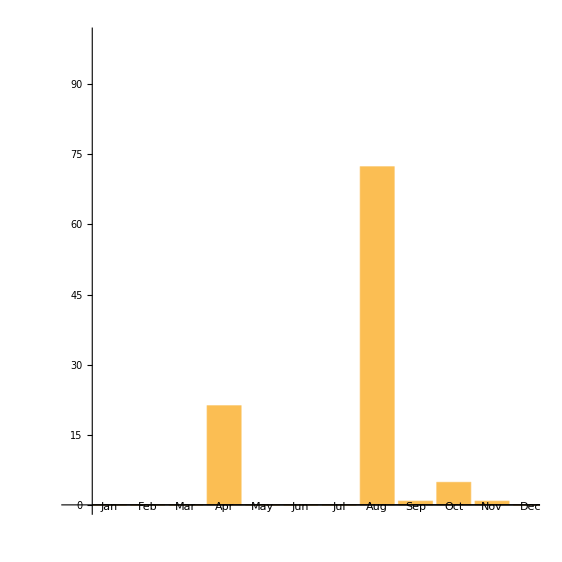

```mathematica
BarChart[Table[100 *posteriors[[j]], {j, 1, 12}], PlotRange->{{0, 12},{0, 100}}, ChartLabels->months, PlotRangePadding->1.0, FrameLabel->{"Posterior (%)"}, AspectRatio->1, ImagePadding->50]
```

If your answer looks significantly different from this, I am not concerned as long as you did all the steps. The difference between your answer an my answer, if you did the steps correctly, is likely from eyeballing the likelihoods in Step 2. Although the pollen count plot was beautiful, it is admittedly hard to go from it to an estimate of what fraction of the time Ambrosia concentrations exceeded Gramineae / Poaceae concentrations.